# Versuch 31

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

```mathematica
ungewichteterReg[xdata_,ydata_]:=Module[{sx2=Total[xdata^2],sy=Total[ydata],sx=Total[xdata],sxy=Sum[xdata[[i]]ydata[[i]],{i,1,Length[xdata]}], n=Length[xdata],Δ,a,b,σ},Δ=(n sx2-sx^2);a=1/Δ(sx2 sy-sx sxy); b=1/Δ(n sxy-sx sy);σ=Sqrt[1/(n-2) Sum[(ydata[[i]]-a - b xdata[[i]])^2,{i,1,n}]];{a,b,σ Sqrt[sx2/Δ], σ Sqrt[n/Δ]}]
```

```mathematica
f[{a_,b_}]:=Quiet[StringReplace[ToString[TeXForm[NumberForm[SetAccuracy[a±b,Accuracy[SetPrecision[b,2]]],ExponentFunction->(Null&)]]],"."->","]]
```

## Import Data

```mathematica
rawData=Import[NotebookDirectory[]<>"Eisenkern lnagsam, 100 mVs 2 (bessere Kurve).txt"];
```

```mathematica
data=Map[StringReplace["E"->"*10^"],Map[StringReplace[","->"."],StringSplit[StringSplit[rawData,"\n"],"	"]]][[2;;]];
```

```mathematica
data=Map[ToExpression,data,{2}];
```

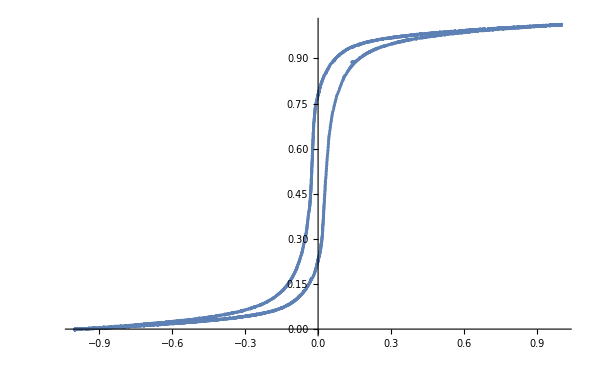

```mathematica
ListPlot[data[[All,{2,3}]]]
```

## Parameters

```mathematica
da=260*10^(-3);
di=220*10^(-3);
h=30*10^(-3);
```

```mathematica
N1=1010;
d=(da+di)/2;
R=0.2;
```

```mathematica
dR=0.01
```

0.01

```mathematica
N2=53;
A=h (da-di)/2;
messbereich=100;
fullfaktor=1;
```

```mathematica
dataProcessed={N1 #[[1]]/(π d R),(messbereich/1000)((#1⟦2⟧)/(N2 fullfaktor A))}&/@data[[All,{2,3}]];
```

```mathematica
xpos = (Max[dataProcessed[[All,1]]]+Min[dataProcessed[[All,1]]])/2
ypos = (Max[dataProcessed[[All,2]]]+Min[dataProcessed[[All,2]]])/2
```

6.69777

1.58962

```mathematica
dataShifted={#[[1]]-xpos,#[[2]]-ypos}&/@dataProcessed;
```

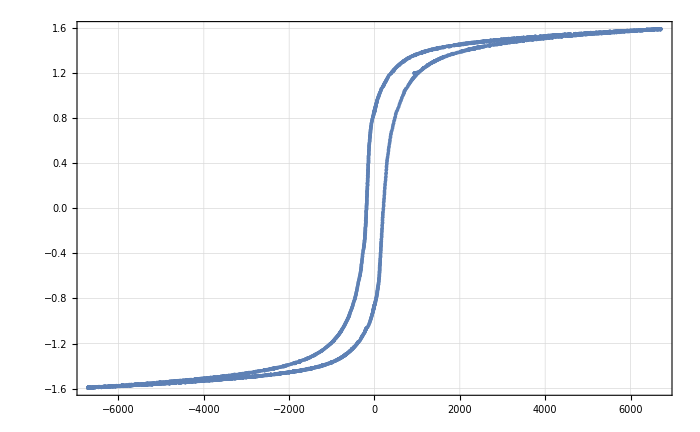

```mathematica
ListPlot[dataShifted,pltsettings]
```

## Remanence & Coercivity

```mathematica
sortedx=SortBy[dataShifted,Abs[Last[#]]&];
```

```mathematica
reg1data=DeleteCases[sortedx,x_/;x[[1]]<0][[1;;10]];
fit1=LinearModelFit[reg1data,x,x];
pars1=ungewichteterReg[reg1data[[All,1]],reg1data[[All,2]]];
reg2data=DeleteCases[sortedx,x_/;x[[1]]>0][[1;;10]];
fit2=LinearModelFit[reg2data,x,x];
pars2=ungewichteterReg[reg2data[[All,1]],reg2data[[All,2]]];
```

```mathematica
sortedy=SortBy[dataShifted,Abs[First[#]]&];
```

```mathematica
reg3data=DeleteCases[sortedy,x_/;x[[2]]<0][[1;;60]];
fit3=LinearModelFit[reg3data,x,x];
pars3=ungewichteterReg[reg3data[[All,1]],reg3data[[All,2]]];
reg4data=DeleteCases[sortedy,x_/;x[[2]]>0][[1;;30]];
fit4=LinearModelFit[reg4data,x,x];
pars4=ungewichteterReg[reg4data[[All,1]],reg4data[[All,2]]];
```

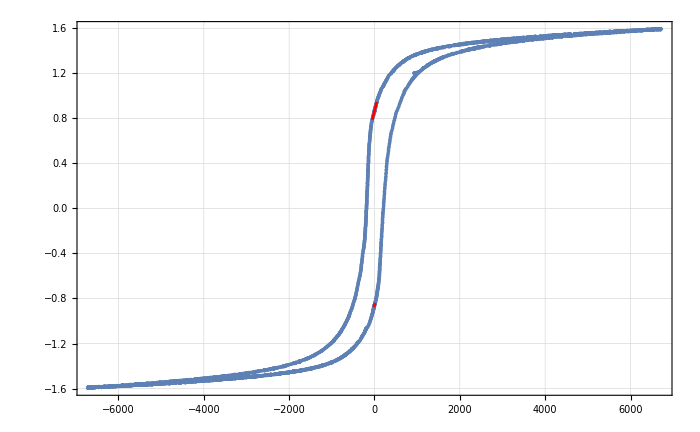

```mathematica
Show[ListPlot[dataShifted],Plot[fit1[x],{x,Min[reg1data[[All,1]]],Max[reg1data[[All,1]]]}],Plot[fit2[x],{x,Min[reg2data[[All,1]]],Max[reg2data[[All,1]]]}],Plot[fit3[x],{x,Min[reg3data[[All,1]]],Max[reg3data[[All,1]]]},PlotStyle->Red],Plot[fit4[x],{x,Min[reg4data[[All,1]]],Max[reg4data[[All,1]]]},PlotStyle->Red],pltsettings]
```

```mathematica
pltHeights=0.4;
```

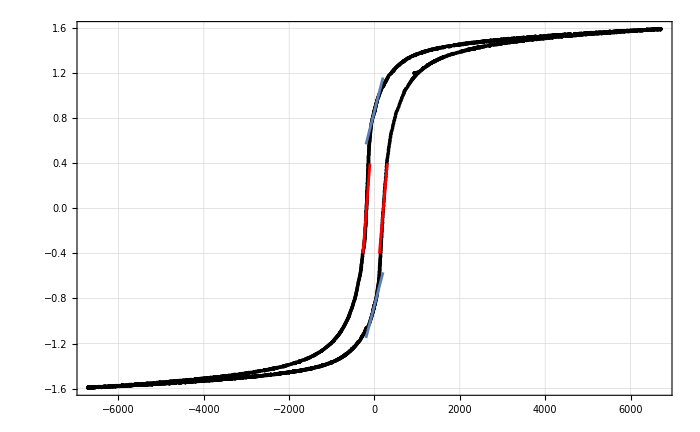

```mathematica
Show[ListPlot[dataShifted,PlotStyle->Black],Plot[fit1[x],{x,InverseFunction[fit1][-pltHeights],InverseFunction[fit1][pltHeights]},PlotStyle->Red],Plot[fit2[x],{x,InverseFunction[fit2][-pltHeights],InverseFunction[fit2][pltHeights]},PlotStyle->Red],Plot[fit3[x],{x,-200,200}],Plot[fit4[x],{x,-200,200}],pltsettings]
```

```mathematica
Export[NotebookDirectory[]<>"abbildungen/Eisenkern raw.pdf",Show[ListPlot[dataShifted,PlotStyle->Black],Plot[fit1[x],{x,InverseFunction[fit1][-pltHeights],InverseFunction[fit1][pltHeights]},PlotStyle->Red],Plot[fit2[x],{x,InverseFunction[fit2][-pltHeights],InverseFunction[fit2][pltHeights]},PlotStyle->Red],Plot[fit3[x],{x,-200,200}],Plot[fit4[x],{x,-200,200}],pltsettings],Background->None];
```

## Remance and coercitivity

```mathematica
Brp=pars3[[1]]
dBrp=pars3[[3]]
Brm=pars4[[1]]
dBrm=pars3[[3]]
```

0.86658

0.000497698

-0.858897

0.000497698

```mathematica
f[{Brp, dBrp}]
f[{Brm, dBrm}]
```

0,86658\pm 0,00050

-0,85890\pm 0,00050

```mathematica
Hm=pars2[[1]]/pars2[[2]]
```

189.158

```mathematica
dHm=Abs[pars2[[1]]/pars2[[2]]]Sqrt[(pars2[[3]]/pars2[[1]])^2 +(pars2[[4]]/pars2[[2]])^2 ]
```

68.2956

```mathematica
Hp=pars1[[1]]/pars1[[2]]
```

-206.803

```mathematica
dHp=Abs[pars1[[1]]/pars1[[2]]]Sqrt[(pars1[[3]]/pars1[[1]])^2 +(pars1[[4]]/pars1[[2]])^2 ]
```

26.2082

```mathematica
f[{Hm, dHm}]
f[{Hp, dHp}]
```

189,\pm 68,

-207,\pm 26,

### Average Values

```mathematica
NumberForm[(Brp/dBrp^2 +Abs@Brm/dBrm^2)/(1/dBrp^2 + 1/dBrm^2),10]
1/Sqrt[(1/dBrp^2 + 1/dBrm^2)]
```

0.8627388152

0.000351926

```mathematica
f[{(Brp/dBrp^2 +Abs@Brm/dBrm^2)/(1/dBrp^2 + 1/dBrm^2), 1/Sqrt[(1/dBrp^2 + 1/dBrm^2)]}]
```

0,86274\pm 0,00035

```mathematica
(Abs@Hp/dHp^2 +Hm/dHm^2)/(1/dHp^2 + 1/dHm^2)
Sqrt[1/(1/dHp^2 + 1/dHm^2)]
```

204.538

24.4684

```mathematica
f[{(Abs@Hp/dHp^2 +Hm/dHm^2)/(1/dHp^2 + 1/dHm^2), Sqrt[1/(1/dHp^2 + 1/dHm^2)]}]
```

205,\pm 24,

### New Computations

```mathematica
dHm=Hm*dR/R
```

9.4579

```mathematica
dHp=Abs[Hp]*dR/R
```

10.3401

```mathematica
f[{Hm, dHm}]
f[{Hp, dHp}]
```

189,2\pm 9,5

-207,\pm 10,

```mathematica
Hbest=(Abs[Hm]+Abs[Hp])/2;
```

```mathematica
dHbest=Max[{Abs[Hbest-(Abs[Hm]-dHm)],Abs[Hbest-(Abs[Hm]+dHm)],Abs[Hbest-(Abs[Hp]-dHp)],Abs[Hbest-(Abs[Hp]+dHp)]}]
```

19.1626

```mathematica
f[{Hbest,dHbest}]
```

198,\pm 19,

```mathematica
extractedB=DeleteCases[dataShifted,x_/;Abs[x[[1]]]>dHbest];
```

```mathematica
dBrp=(Max[#]-Min[#]&)[DeleteCases[extractedB,x_/;x[[2]]<0][[All,2]]]
```

0.0408805

```mathematica
dBrm=(Max[#]-Min[#]&)[DeleteCases[extractedB,x_/;x[[2]]>0][[All,2]]]
```

0.0440252

```mathematica
BBest=(Abs[Brp]+Abs[Brm])/2;
```

```mathematica
f[{Brp, dBrp}]
f[{Brm, dBrm}]
```

0,867\pm 0,041

-0,859\pm 0,044

```mathematica
dBbest=Max[{Abs[BBest-(Abs[Brp]-dBrp)],Abs[BBest-(Abs[Brp]+dBrp)],Abs[BBest-(Abs[Brm]-dBrm)],Abs[BBest-(Abs[Brm]+dBrm)]}]
```

0.0478666

```mathematica
f[{BBest, dBbest}]
```

0,863\pm 0,048